# Distance between two parallel lines

```mathematica
Subscript[x, P_]:=P[[1]];Subscript[y, P_]:=P[[2]];
```

```mathematica
y1[x_]=2x-2;
```

```mathematica
y2[x_]=2x+2;
```

```mathematica
P={0,y2[0]}
```

{0,2}

```mathematica
A=Coefficient[y1[x],x, 1];B=-1;𝒞=Coefficient[y1[x],x, 0];
```

```mathematica
A x +B y+𝒞==0
```

-2+2 x-y==0

```mathematica
d=Abs[A Subscript[x, P]+B Subscript[y, P]+𝒞]/(√(A^2+B^2))
```

4/(√5)

```mathematica
PointP=ListPlot[{P},PlotRange->{{-5,5},{-5,5}},MeshStyle->Red,PlotMarkers->{Automatic,Medium},AspectRatio->1];
```

```mathematica
LineD1=Plot[y1[x],{x,-5,5},PlotRange->{{-5,5},{-5,5}},AspectRatio->1];
```

```mathematica
LineD2=Plot[y2[x],{x,-5,5},PlotRange->{{-5,5},{-5,5}},AspectRatio->1];
```

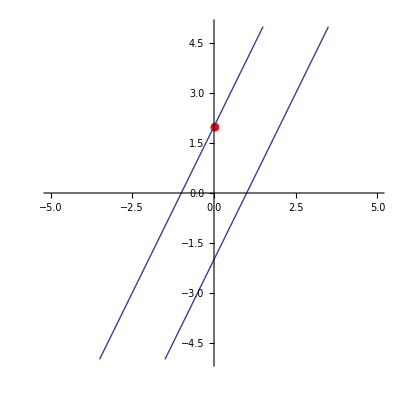

```mathematica
Show[PointP,LineD1,LineD2]
```